## Реализация алгоритмов поиска наименьшего пути в графе

```mathematica
SetDirectory[NotebookDirectory[]];
problem=Import["Practice-3-term/examples/problem.txt", "Table"];
solution =Import["Practice-3-term/examples/solution.txt", "Table"];
```

```mathematica
nNodes=problem[[1]]/.{x_}->x;
nodes = Table[problem[[i]], {i,2, nNodes+1}];
nEdges=problem[[nNodes+2]]/.{x_}->x;
edges= Table[problem[[i]], {i,nNodes+3, nEdges+nNodes+2}];
nRoads=problem[[nEdges+nNodes+3]]/.{x_}->x;
roads =Table[problem[[i]],{i, nEdges+nNodes+4, nRoads+nEdges+nNodes+3}];
```

Реализация через встроенные возможности Mathematica:

```mathematica
graph=Graph[edges/.{a_, b_, c_}->{a, b}, DirectedEdges->True,EdgeWeight->Table[edges[[i]][[3]], {i,nEdges}] (*EdgeLabels->"EdgeWeight"*)]
```

-Graphics-

```mathematica
solution=Table[FindShortestPath[graph,roads[[i]][[1]],roads[[i]][[2]], Method->"BellmanFord"],{i,nRoads}]
Table[HighlightGraph[graph,PathGraph[solution[[i]]]], {i, nRoads}]
```

{{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24},{24,54,86,105,115,122,124,118,94,63,5}}

{-Graphics-,-Graphics-}

Реализация методом Беллмана - Форда:

{{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24},{24,54,86,105,115,122,124,118,94,63,5}}

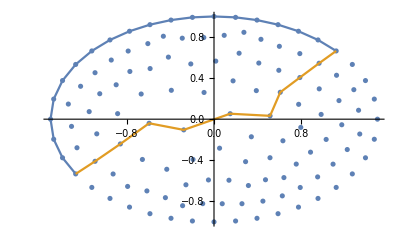

```mathematica
BellmanFord[g_?WeightedGraphQ,v1_?IntegerQ, v2_ ?IntegerQ]:=Block[
{
INF=1000000000, 
distance= Table[INF, nNodes],
routes=Table[0, nNodes],
path=Table[0, nNodes],
any,
EdgeW=AnnotationValue[g,EdgeWeight],
EdgeL=EdgeList[g],
t=1
},

distance[[v1]]=0;

While[True,
any=False;
For[j=1,j<nEdges+1,j++,
If[(distance[[ EdgeL[[j]][[1]] ]]<INF)&&(distance[[EdgeL[[j]][[2]]]]>distance[[EdgeL[[j]][[1]]]]+EdgeW[[j]]), 
distance[[EdgeL[[j]][[2]]]]=distance[[EdgeL[[j]][[1]]]]+EdgeW[[j]];
routes[[EdgeL[[j]][[2]]]]=EdgeL[[j]][[1]];
any=True
]
];
If[Not[any],Break[]];
];

For[i=v2, i!=-1, i=routes[[i]],
path[[nNodes-t+1]]=i;
t++
];

Return[Cases[path,Except[0]]];
];
solution=Table[BellmanFord[graph, roads[[i]][[1]],roads[[i]][[2]]],{i, nRoads}]
solutionRoad=Table[Table[nodes[[ solution[[j]][[i]] ]],{i, Length[solution[[j]]]}],{j,nRoads}];
Show[ListPlot[nodes],
ListLinePlot[solutionRoad]]
```

Реализация методом перебора